# Berechnung der Stetigkeitsbedingungen der Wellenfunktion bei M=0

Stetigkeitsmatrix aus vorherigem Mathematica-Notebook

```mathematica
M=({{-(ⅇ^((ⅈ L (√(-Δ^2+ϵ^2)+μ))/(v ℏ)) (ϵ+√(-Δ^2+ϵ^2)))/Δ, (ⅇ^((ⅈ L (√(-Δ^2+ϵ^2)-μ))/(v ℏ)) (ϵ-√(-Δ^2+ϵ^2)))/Δ, 0, -ⅇ^(-(ⅈ L (ϵ+μ))/(v ℏ)), ⅇ^((ⅈ L (ϵ+μ))/(v ℏ)), 0, 0, 0}, {(ⅇ^((ⅈ L (√(-Δ^2+ϵ^2)+μ))/(v ℏ)) (ϵ+√(-Δ^2+ϵ^2)))/Δ, (ⅇ^((ⅈ L (√(-Δ^2+ϵ^2)-μ))/(v ℏ)) (ϵ-√(-Δ^2+ϵ^2)))/Δ, 0, -ⅇ^(-(ⅈ L (ϵ+μ))/(v ℏ)), -ⅇ^((ⅈ L (ϵ+μ))/(v ℏ)), 0, 0, 0}, {-ⅇ^((ⅈ L (√(-Δ^2+ϵ^2)+μ))/(v ℏ)), ⅇ^((ⅈ L (√(-Δ^2+ϵ^2)-μ))/(v ℏ)), ⅇ^(-(ⅈ L (ϵ-μ))/(v ℏ)), 0, 0, -ⅇ^((ⅈ L (ϵ-μ))/(v ℏ)), 0, 0}, {ⅇ^((ⅈ L (√(-Δ^2+ϵ^2)+μ))/(v ℏ)), ⅇ^((ⅈ L (√(-Δ^2+ϵ^2)-μ))/(v ℏ)), -ⅇ^(-(ⅈ L (ϵ-μ))/(v ℏ)), 0, 0, -ⅇ^((ⅈ L (ϵ-μ))/(v ℏ)), 0, 0}, {0, 0, 0, -ⅇ^((ⅈ L (ϵ+μ))/(v ℏ)), ⅇ^(-(ⅈ L (ϵ+μ))/(v ℏ)), 0, (ⅇ^(-ⅈ ϕ+(ⅈ L (√(-Δ^2+ϵ^2)-μ))/(v ℏ)) (-ϵ+√(-Δ^2+ϵ^2)))/Δ, (ⅇ^(-ⅈ ϕ+(ⅈ L (√(-Δ^2+ϵ^2)+μ))/(v ℏ)) (ϵ+√(-Δ^2+ϵ^2)))/Δ}, {0, 0, 0, -ⅇ^((ⅈ L (ϵ+μ))/(v ℏ)), -ⅇ^(-(ⅈ L (ϵ+μ))/(v ℏ)), 0, (ⅇ^(-ⅈ ϕ+(ⅈ L (√(-Δ^2+ϵ^2)-μ))/(v ℏ)) (ϵ-√(-Δ^2+ϵ^2)))/Δ, (ⅇ^(-ⅈ ϕ+(ⅈ L (√(-Δ^2+ϵ^2)+μ))/(v ℏ)) (ϵ+√(-Δ^2+ϵ^2)))/Δ}, {0, 0, ⅇ^((ⅈ L (ϵ-μ))/(v ℏ)), 0, 0, -ⅇ^(-(ⅈ L (ϵ-μ))/(v ℏ)), -ⅇ^((ⅈ L (√(-Δ^2+ϵ^2)-μ))/(v ℏ)), ⅇ^((ⅈ L (√(-Δ^2+ϵ^2)+μ))/(v ℏ))}, {0, 0, -ⅇ^((ⅈ L (ϵ-μ))/(v ℏ)), 0, 0, -ⅇ^(-(ⅈ L (ϵ-μ))/(v ℏ)), ⅇ^((ⅈ L (√(-Δ^2+ϵ^2)-μ))/(v ℏ)), ⅇ^((ⅈ L (√(-Δ^2+ϵ^2)+μ))/(v ℏ))}});
ψ={a,b,c,d,e,f,g,h};
```

```mathematica
A=FullSimplify[M.ψ];
MatrixForm[A]
```

((ⅇ^(-(ⅈ L (ϵ+μ))/(v ℏ)) (-d Δ+e ⅇ^((2 ⅈ L (ϵ+μ))/(v ℏ)) Δ-ⅇ^((ⅈ L (ϵ+√(-Δ^2+ϵ^2)))/(v ℏ)) (b (-ϵ+√(-Δ^2+ϵ^2))+a ⅇ^((2 ⅈ L μ)/(v ℏ)) (ϵ+√(-Δ^2+ϵ^2)))))/Δ
(ⅇ^(-(ⅈ L (ϵ+μ))/(v ℏ)) (-d Δ-e ⅇ^((2 ⅈ L (ϵ+μ))/(v ℏ)) Δ+ⅇ^((ⅈ L (ϵ+√(-Δ^2+ϵ^2)))/(v ℏ)) (b (ϵ-√(-Δ^2+ϵ^2))+a ⅇ^((2 ⅈ L μ)/(v ℏ)) (ϵ+√(-Δ^2+ϵ^2)))))/Δ
c ⅇ^(-(ⅈ L (ϵ-μ))/(v ℏ))+b ⅇ^((ⅈ L (√(-Δ^2+ϵ^2)-μ))/(v ℏ))-a ⅇ^((ⅈ L (√(-Δ^2+ϵ^2)+μ))/(v ℏ))-ⅇ^((ⅈ L (ϵ-μ))/(v ℏ)) f
-c ⅇ^(-(ⅈ L (ϵ-μ))/(v ℏ))+b ⅇ^((ⅈ L (√(-Δ^2+ϵ^2)-μ))/(v ℏ))+a ⅇ^((ⅈ L (√(-Δ^2+ϵ^2)+μ))/(v ℏ))-ⅇ^((ⅈ L (ϵ-μ))/(v ℏ)) f
(ⅇ^(-ⅈ (ϕ+(L (ϵ+μ))/(v ℏ))) (e ⅇ^(ⅈ ϕ) Δ-d ⅇ^(ⅈ (ϕ+(2 L (ϵ+μ))/(v ℏ))) Δ+ⅇ^((ⅈ L (ϵ+√(-Δ^2+ϵ^2)))/(v ℏ)) (g (-ϵ+√(-Δ^2+ϵ^2))+ⅇ^((2 ⅈ L μ)/(v ℏ)) h (ϵ+√(-Δ^2+ϵ^2)))))/Δ
(ⅇ^(-ⅈ (ϕ+(L (ϵ+μ))/(v ℏ))) (-e ⅇ^(ⅈ ϕ) Δ-d ⅇ^(ⅈ (ϕ+(2 L (ϵ+μ))/(v ℏ))) Δ+ⅇ^((ⅈ L (ϵ+√(-Δ^2+ϵ^2)))/(v ℏ)) (g (ϵ-√(-Δ^2+ϵ^2))+ⅇ^((2 ⅈ L μ)/(v ℏ)) h (ϵ+√(-Δ^2+ϵ^2)))))/Δ
c ⅇ^((ⅈ L (ϵ-μ))/(v ℏ))-ⅇ^(-(ⅈ L (ϵ-μ))/(v ℏ)) f-ⅇ^((ⅈ L (√(-Δ^2+ϵ^2)-μ))/(v ℏ)) g+ⅇ^((ⅈ L (√(-Δ^2+ϵ^2)+μ))/(v ℏ)) h
-c ⅇ^((ⅈ L (ϵ-μ))/(v ℏ))-ⅇ^(-(ⅈ L (ϵ-μ))/(v ℏ)) f+ⅇ^((ⅈ L (√(-Δ^2+ϵ^2)-μ))/(v ℏ)) g+ⅇ^((ⅈ L (√(-Δ^2+ϵ^2)+μ))/(v ℏ)) h)

Addieren und Subtrahieren der einzelnen Gleichungen zur Vereinfachung

```mathematica
AA={
FullSimplify[A[[1]]+A[[2]]],
FullSimplify[A[[1]]-A[[2]]],
FullSimplify[A[[3]]+A[[4]]],
FullSimplify[A[[3]]-A[[4]]],
FullSimplify[A[[5]]+A[[6]]],
FullSimplify[A[[5]]-A[[6]]],
FullSimplify[A[[7]]+A[[8]]],
FullSimplify[A[[7]]-A[[8]]]
};
MatrixForm[AA]
```

(-(2 ⅇ^(-(ⅈ L (ϵ+μ))/(v ℏ)) (d Δ+b ⅇ^((ⅈ L (ϵ+√(-Δ^2+ϵ^2)))/(v ℏ)) (-ϵ+√(-Δ^2+ϵ^2))))/Δ
2 e ⅇ^((ⅈ L (ϵ+μ))/(v ℏ))-(2 a ⅇ^((ⅈ L (√(-Δ^2+ϵ^2)+μ))/(v ℏ)) (ϵ+√(-Δ^2+ϵ^2)))/Δ
2 b ⅇ^((ⅈ L (√(-Δ^2+ϵ^2)-μ))/(v ℏ))-2 ⅇ^((ⅈ L (ϵ-μ))/(v ℏ)) f
2 c ⅇ^(-(ⅈ L (ϵ-μ))/(v ℏ))-2 a ⅇ^((ⅈ L (√(-Δ^2+ϵ^2)+μ))/(v ℏ))
(ⅇ^(-ⅈ (ϕ+(L (ϵ+μ))/(v ℏ))) (-2 d ⅇ^(ⅈ (ϕ+(2 L (ϵ+μ))/(v ℏ))) Δ+2 ⅇ^((ⅈ L (ϵ+√(-Δ^2+ϵ^2)+2 μ))/(v ℏ)) h (ϵ+√(-Δ^2+ϵ^2))))/Δ
(2 ⅇ^(-ⅈ (ϕ+(L (ϵ+μ))/(v ℏ))) (e ⅇ^(ⅈ ϕ) Δ+ⅇ^((ⅈ L (ϵ+√(-Δ^2+ϵ^2)))/(v ℏ)) g (-ϵ+√(-Δ^2+ϵ^2))))/Δ
-2 ⅇ^(-(ⅈ L (ϵ-μ))/(v ℏ)) f+2 ⅇ^((ⅈ L (√(-Δ^2+ϵ^2)+μ))/(v ℏ)) h
2 c ⅇ^((ⅈ L (ϵ-μ))/(v ℏ))-2 ⅇ^((ⅈ L (√(-Δ^2+ϵ^2)-μ))/(v ℏ)) g)

```mathematica
solD=Solve[AA[[1]]==0,d][[1,1]];
solE=Solve[AA[[2]]==0,e][[1,1]];
solF=Solve[AA[[3]]==0,f][[1,1]];
solC=Solve[AA[[4]]==0,c][[1,1]];
solH=Solve[AA[[5]]==0,h][[1,1]]/.solD;
solG=Solve[AA[[6]]==0,g][[1,1]]/.solE;
Solve[AA[[7]]==0,f][[1,1]]/.solH
Solve[AA[[8]]==0,c][[1,1]]/.solG
solveVecAB=FullSimplify[{solC,solD,solE,solF,solG,solH}];
MatrixForm[solveVecAB]
```

f→-(b ⅇ^(ⅈ ϕ+(ⅈ L (ϵ+√(-Δ^2+ϵ^2)))/(v ℏ)+(ⅈ L (ϵ-μ))/(v ℏ)+(2 ⅈ L (ϵ+μ))/(v ℏ)+(ⅈ L (√(-Δ^2+ϵ^2)+μ))/(v ℏ)-(ⅈ L (ϵ+√(-Δ^2+ϵ^2)+2 μ))/(v ℏ)) (-ϵ+√(-Δ^2+ϵ^2)))/(ϵ+√(-Δ^2+ϵ^2))

c→-(a ⅇ^(ⅈ ϕ-(ⅈ L (ϵ+√(-Δ^2+ϵ^2)))/(v ℏ)-(ⅈ L (ϵ-μ))/(v ℏ)+(ⅈ L (√(-Δ^2+ϵ^2)-μ))/(v ℏ)-(ⅈ L (ϵ+μ))/(v ℏ)+(ⅈ L (√(-Δ^2+ϵ^2)+μ))/(v ℏ)) (ϵ+√(-Δ^2+ϵ^2)))/(-ϵ+√(-Δ^2+ϵ^2))

(c→a ⅇ^((ⅈ L (ϵ+√(-Δ^2+ϵ^2)))/(v ℏ))
d→-(b ⅇ^((ⅈ L (ϵ+√(-Δ^2+ϵ^2)))/(v ℏ)) (-ϵ+√(-Δ^2+ϵ^2)))/Δ
e→(a ⅇ^((ⅈ L (-ϵ+√(-Δ^2+ϵ^2)))/(v ℏ)) (ϵ+√(-Δ^2+ϵ^2)))/Δ
f→b ⅇ^((ⅈ L (-ϵ+√(-Δ^2+ϵ^2)))/(v ℏ))
g→(a ⅇ^(ⅈ (ϕ-(2 L ϵ)/(v ℏ))) (-Δ^2+2 ϵ (ϵ+√(-Δ^2+ϵ^2))))/Δ^2
h→-(b ⅇ^(ⅈ (ϕ+(2 L ϵ)/(v ℏ))) (Δ^2+2 ϵ (-ϵ+√(-Δ^2+ϵ^2))))/Δ^2)

```mathematica
ψneu=ψ/. solveVecAB;
MatrixForm[ψneu]
test1=FullSimplify[M.ψneu];
MatrixForm[test1]
Solve[test1==0,{a,b}]
```

(a
b
a ⅇ^((ⅈ L (ϵ+√(-Δ^2+ϵ^2)))/(v ℏ))
-(b ⅇ^((ⅈ L (ϵ+√(-Δ^2+ϵ^2)))/(v ℏ)) (-ϵ+√(-Δ^2+ϵ^2)))/Δ
(a ⅇ^((ⅈ L (-ϵ+√(-Δ^2+ϵ^2)))/(v ℏ)) (ϵ+√(-Δ^2+ϵ^2)))/Δ
b ⅇ^((ⅈ L (-ϵ+√(-Δ^2+ϵ^2)))/(v ℏ))
(a ⅇ^(ⅈ (ϕ-(2 L ϵ)/(v ℏ))) (-Δ^2+2 ϵ (ϵ+√(-Δ^2+ϵ^2))))/Δ^2
-(b ⅇ^(ⅈ (ϕ+(2 L ϵ)/(v ℏ))) (Δ^2+2 ϵ (-ϵ+√(-Δ^2+ϵ^2))))/Δ^2)

(0
0
0
0
0
0
(ⅇ^((ⅈ L (-2 ϵ+√(-Δ^2+ϵ^2)-μ))/(v ℏ)) (-b ⅇ^((2 ⅈ L μ)/(v ℏ)) ((1+ⅇ^(ⅈ (ϕ+(4 L ϵ)/(v ℏ)))) Δ^2+2 ⅇ^(ⅈ (ϕ+(4 L ϵ)/(v ℏ))) ϵ (-ϵ+√(-Δ^2+ϵ^2)))+a (ⅇ^((4 ⅈ L ϵ)/(v ℏ)) Δ^2+ⅇ^(ⅈ ϕ) (Δ^2-2 ϵ (ϵ+√(-Δ^2+ϵ^2))))))/Δ^2
-(ⅇ^((ⅈ L (-2 ϵ+√(-Δ^2+ϵ^2)-μ))/(v ℏ)) (b ⅇ^((2 ⅈ L μ)/(v ℏ)) ((1+ⅇ^(ⅈ (ϕ+(4 L ϵ)/(v ℏ)))) Δ^2+2 ⅇ^(ⅈ (ϕ+(4 L ϵ)/(v ℏ))) ϵ (-ϵ+√(-Δ^2+ϵ^2)))+a (ⅇ^((4 ⅈ L ϵ)/(v ℏ)) Δ^2+ⅇ^(ⅈ ϕ) (Δ^2-2 ϵ (ϵ+√(-Δ^2+ϵ^2))))))/Δ^2)

{{a→0,b→0}}

Numerische Überprüfung. Ergebnis: {(a=0,b=1),(a=1,b=0)}
letzter EW =0 -> betrachte letzten EV

```mathematica
M/.{L->0,v->1,ϵ->0.1,Δ->1,ℏ->1,µ->1,ϕ->2ArcCos[0.1]};
N[Eigensystem[(M/.ϕ->-ArcCos[-((Δ^2-2 ϵ^2) Cos[(4 L ϵ)/(v ℏ)]+2 ⅈ ϵ √(-Δ^2+ϵ^2) Sin[(4 L ϵ)/(v ℏ)])/Δ^2])/.{L->1,v->1,ϵ->-0.1,Δ->1,ℏ->1,μ->1}]]
```

{{0.486989+1.57894 ⅈ,1.56803-0.261531 ⅈ,0.426586-1.3897 ⅈ,-1.06375+0.23229 ⅈ,-0.785917-0.178887 ⅈ,0.378356+0.0940558 ⅈ,0.0649141+0.319645 ⅈ,-4.18193×10^-16+5.96498×10^-16 ⅈ},{{-0.220017+0.0595646 ⅈ,-0.00601276+0.03758 ⅈ,0.229368-0.515562 ⅈ,-0.0253073+0.198822 ⅈ,-0.176739-0.131381 ⅈ,-0.0647221-0.291622 ⅈ,-0.195374+0.264166 ⅈ,0.585087+0. ⅈ},{-0.341258-0.139836 ⅈ,0.0310512+0.356577 ⅈ,0.0330582+0.339771 ⅈ,0.425367+0. ⅈ,-0.41277-0.0455391 ⅈ,-0.00094004-0.321223 ⅈ,-0.0233039+0.0652409 ⅈ,-0.37667-0.126825 ⅈ},{0.514714+0. ⅈ,-0.0435613+0.370007 ⅈ,0.0210266-0.159305 ⅈ,-0.279637-0.137083 ⅈ,-0.489323+0.00443074 ⅈ,0.19256+0.314376 ⅈ,0.168783-0.0370215 ⅈ,0.19032+0.178911 ⅈ},{-0.10612-0.397024 ⅈ,-0.0940397-0.206631 ⅈ,-0.0677577-0.21522 ⅈ,0.0555742-0.274176 ⅈ,0.247626+0.0304551 ⅈ,0.175027-0.253347 ⅈ,0.680151+0. ⅈ,-0.0313726+0.172464 ⅈ},{0.0894928-0.513827 ⅈ,0.0836151-0.378758 ⅈ,0.081297-0.20434 ⅈ,0.211146-0.0950348 ⅈ,0.211823+0.11414 ⅈ,0.190545-0.0514691 ⅈ,0.585422+0. ⅈ,-0.0395515+0.185499 ⅈ},{-0.209334-0.267696 ⅈ,0.539274-0.0181735 ⅈ,-0.0565692-0.0817503 ⅈ,-0.123593-0.22952 ⅈ,-0.0329042-0.00565563 ⅈ,0.147849+0.0611019 ⅈ,0.00137249+0.118526 ⅈ,0.68904+0. ⅈ},{0.163136-0.0444132 ⅈ,0.415509-0.285755 ⅈ,0.0769722+0.0274526 ⅈ,-0.114516-0.236423 ⅈ,-0.0504277+0.078804 ⅈ,0.137417-0.112667 ⅈ,0.140626+0.324636 ⅈ,0.689876+0. ⅈ},{3.61267×10^-16-8.61172×10^-16 ⅈ,0.650007-0.131763 ⅈ,2.07251×10^-16+2.52839×10^-16 ⅈ,-0.0955285-0.225841 ⅈ,-1.60666×10^-17-7.24171×10^-16 ⅈ,0.243989-0.0244805 ⅈ,9.91483×10^-17+8.87202×10^-17 ⅈ,0.663227+0. ⅈ}}}

Zeigen, dass die Faktoren individuell 0 sind, damit M*EV = 0 gilt für {(a=0,b=1),(a=1,b=0)}

1. Komponente = 2. Komponente:

```mathematica
-b ⅇ^((2 ⅈ L μ)/(v ℏ)) ((1+ⅇ^(ⅈ (ϕ+(4 L ϵ)/(v ℏ)))) Δ^2+2 ⅇ^(ⅈ (ϕ+(4 L ϵ)/(v ℏ))) ϵ (-ϵ+√(-Δ^2+ϵ^2)))+a (ⅇ^((4 ⅈ L ϵ)/(v ℏ)) Δ^2+ⅇ^(ⅈ ϕ) (Δ^2-2 ϵ (ϵ+√(-Δ^2+ϵ^2))))==0;
```

für b=0; für alle a:

```mathematica
ⅇ^((4 ⅈ L ϵ)/(v ℏ)) Δ^2+ⅇ^(ⅈ ϕ) (Δ^2-2 ϵ (ϵ+√(-Δ^2+ϵ^2)))==0;
```

2. Term: a=0

```mathematica
-b ⅇ^((2 ⅈ L μ)/(v ℏ)) ((1+ⅇ^(ⅈ (ϕ+(4 L ϵ)/(v ℏ)))) Δ^2+2 ⅇ^(ⅈ (ϕ+(4 L ϵ)/(v ℏ))) ϵ (-ϵ+√(-Δ^2+ϵ^2)))==0;
(1+ⅇ^(ⅈ (ϕ+(4 L ϵ)/(v ℏ)))) Δ^2+2 ⅇ^(ⅈ (ϕ+(4 L ϵ)/(v ℏ))) ϵ (-ϵ+√(-Δ^2+ϵ^2))==0;
Δ^2+Δ^2 ⅇ^(ⅈ (ϕ+(4 L ϵ)/(v ℏ)))+2 ⅇ^(ⅈ (ϕ+(4 L ϵ)/(v ℏ))) ϵ (-ϵ+√(-Δ^2+ϵ^2))==0;
Δ^2+ⅇ^(ⅈ (ϕ+(4 L ϵ)/(v ℏ))) (Δ^2-2ϵ (ϵ-√(-Δ^2+ϵ^2)))==0;

Δ^2+ⅇ^ⅈϕ ⅇ^((4 ⅈ L ϵ)/(v ℏ))(Δ^2-2ϵ (ϵ-√(-Δ^2+ϵ^2)))==0;
Δ^2 ⅇ^(-(4 ⅈ L ϵ)/(v ℏ))+ⅇ^ⅈϕ (Δ^2-2ϵ (ϵ-√(-Δ^2+ϵ^2)))==0;
Δ^2 ⅇ^((4 ⅈ L ϵ)/(v ℏ))+ⅇ^-ⅈϕ (Δ^2-2ϵ (ϵ+√(-Δ^2+ϵ^2)))==0;
```

-> 1. und 2. Term identisch

erwartete Lösung aus vorigem Mathematica-Notebook für -Det[M] = 0:

```mathematica
{{ϕ->ConditionalExpression[-ArcCos[-((Δ^2-2 ϵ^2) Cos[(4 L ϵ)/(v ℏ)]+2 ⅈ ϵ √(-Δ^2+ϵ^2) Sin[(4 L ϵ)/(v ℏ)])/Δ^2]+2 π C[1], C[1]∈Integers]},{ϕ->ConditionalExpression[ArcCos[-((Δ^2-2 ϵ^2) Cos[(4 L ϵ)/(v ℏ)]+2 ⅈ ϵ √(-Δ^2+ϵ^2) Sin[(4 L ϵ)/(v ℏ)])/Δ^2]+2 π C[1], C[1]∈Integers]}};
{{Cos[-ϕ]->-((Δ^2-2 ϵ^2) Cos[(4 L ϵ)/(v ℏ)]+2 ⅈ ϵ √(-Δ^2+ϵ^2) Sin[(4 L ϵ)/(v ℏ)])/Δ^2},{Cos[ϕ]->-((Δ^2-2 ϵ^2) Cos[(4 L ϵ)/(v ℏ)]+2 ⅈ ϵ √(-Δ^2+ϵ^2) Sin[(4 L ϵ)/(v ℏ)])/Δ^2}}
```

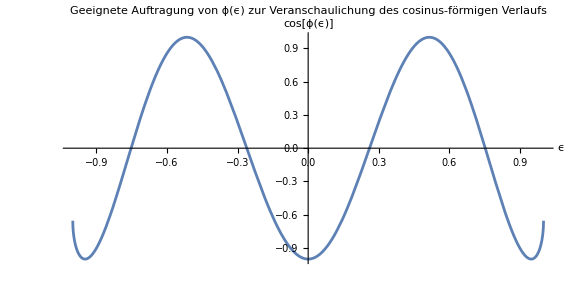

```mathematica
Plot[{-((Δ^2-2 ϵ^2) Cos[(4 L ϵ)/(v ℏ)]+2 ⅈ ϵ √(-Δ^2+ϵ^2) Sin[(4 L ϵ)/(v ℏ)])/Δ^2/.{L->1,v->1,Δ->1,ℏ->1,μ->1}},{ϵ,-1,1},AxesLabel->{"ϵ","cos[ϕ(ϵ)]"},PlotLabel->"Geeignete Auftragung von ϕ(ϵ) zur Veranschaulichung des cosinus-förmigen Verlaufs",PlotRange->Full,AspectRatio->1/2,ImageSize->Large]
```